```mathematica
dPhi=500;Tm=100;
```

```mathematica
vbth[deltaPhi_,T_]:=√(deltaPhi/T);
```

```mathematica
normFacMaxwellian[T_,kappa_]:=(m/(2 π T))^(3/2)
```

```mathematica
normFacKappa[T_,kappa_]:=(m/(2 π T (1 - 3/(2 kappa))))^(3/2)Gamma[kappa+1]/(kappa^(3/2)Gamma[kappa-1/2])
```

```mathematica
dir="/SPENCEdata/Research/Satellites/FAST/kappa_dists/journals/";
SetDirectory[dir];
<<Liemohn_and_Khazanov__mapped_Maxwellian_density.wl
```

Also, here’s the current (not totally working) version of the kappa curve thing

```mathematica
densFacK[phiBar_,κ_,RB_]:=1/(2 √phiBar (-3+2 κ)^(5/2))(phiBar (3+2 phiBar-2 κ)^-κ √((3+2 phiBar-2 κ)/phiBar) (-3+2 κ)^(2+κ) Csc[π κ]+1/(phiBar Gamma[-3/2+κ])2 √(2/π) (1/((-1+RB) (3+2 κ) (-1+4 κ^2))Gamma[1+κ] ((-1+RB) (-3+2 κ) ((-1+RB)^2 (3-2 κ)^2+2 phiBar (-1+RB) (-3+2 κ) (5+2 κ)-4 phiBar^2 (-1+6 κ+4 κ^2))-(2 phiBar+(-1+RB) (-3+2 κ))^3 Hypergeometric2F1[1,1+κ,-1/2,(2 phiBar)/((-1+RB) (3-2 κ))])+2 phiBar^2 π (-3+2 κ) Csc[π κ] Hypergeometric2F1Regularized[-1/2,1,1-κ,(-3+2 κ)/(2 phiBar)]))
```

## Distribution functions at source

#### Step function definition

```mathematica
sourcePieceFuncMax[vpar_,vperp_,vbth_,RB_,potExp_]:=Piecewise[{{1,vperp^2(1-RB)+vpar^2+vbth^2>0&&vpar>0},{0,vpar≤ 0},{0,vperp^2(1-RB)+vpar^2+vbth^2≤ 0}}]
```

```mathematica
sourcePieceFuncKappa[vpar_,vperp_,vbth_,RB_]:=Piecewise[{{1,vperp^2(1-RB)+vpar^2+vbth^2>0&&vpar>0},{0,vpar≤ 0},{0,vperp^2(1-RB)+vpar^2+vbth^2≤ 0}}]
```

#### Kappa function definition

Kappa w/ modified step func, in units s.t. v_th=1

```mathematica
sourceFuncMaxwellian[vpar_,vperp_,vbth_,RB_,potExp_]:=1/π^(3/2)Exp[-(vpar^2+vperp^2+vbth^2)]sourcePieceFuncMax[vpar,vperp,vbth,RB,potExp]
```

```mathematica
sourceFuncKappa[vpar_,vperp_,vbth_,RB_,kappa_]:=1/(π^(3/2)(1-3/(2 kappa))^(3/2))Gamma[kappa+1]/(kappa^(3/2)Gamma[kappa-1/2])(1+(vpar^2+vperp^2+vbth^2)/(kappa-3/2))^(-(kappa+1))sourcePieceFuncKappa[vpar,vperp,vbth,RB]
```

## Distribution functions at bottom of potential drop

```mathematica
bottomPieceFuncKappa[vpar_,vperp_,vbth_,RB_]:=Piecewise[{{1,vperp^2(1-1/RB)+vpar^2-vbth^2>0&&vpar>0},{0,vpar≤ 0},{0,vperp^2(1-1/RB)+vpar^2-vbth^2≤ 0}}]
```

```mathematica
bottomPieceFuncKappaRho[rho_,θ_,phiBar_,RB_]:=Piecewise[{{1,rho^2(1- (Sin[θ])^2/RB)-phiBar>0&&rho≥ 0},{0,rho≤ 0},{0,rho^2(1- (Sin[θ])^2/RB)-phiBar< 0}}]
```

```mathematica
bottomPieceFuncMax[vpar_,vperp_,vbth_,RB_,potExp_]:=Piecewise[{{1,vperp^2(1-1/RB)+vpar^2-vbth^2>0&&vpar>0},{0,vpar≤ 0},{0,vperp^2(1-1/RB)+vpar^2-vbth^2≤ 0}}]
```

```mathematica
bottomPieceFuncMaxRho[rho_,θ_,phiBar_,RB_]:=Piecewise[{{1,rho^2(1- (Sin[θ])^2/RB)-phiBar>0&&rho≥ 0},{0,rho≤ 0},{0,rho^2(1- (Sin[θ])^2/RB)-phiBar< 0}}]
```

```mathematica
bottomFuncMaxwellian[vpar_,vperp_,vbth_,RB_,potExp_]:=1/π^(3/2)Exp[-(vpar^2+vperp^2-vbth^2)]bottomPieceFuncMax[vpar,vperp,vbth,RB,potExp]
```

```mathematica
bottomFuncKappa[vpar_,vperp_,vbth_,RB_,kappa_]:=1/(π^(3/2)(1-3/(2 kappa))^(3/2))Gamma[kappa+1]/(kappa^(3/2)Gamma[kappa-1/2])(1+(vpar^2+vperp^2-vbth^2)/(kappa-3/2))^(-(kappa+1))bottomPieceFuncKappa[vpar,vperp,vbth,RB]
```

```mathematica
MaxwellGrate[RB_,phiBar_]:=2/(√π)NIntegrate[rho^2 Sin[theta] Exp[-rho^2+phiBar]bottomPieceFuncMaxRho[rho,theta,phiBar,RB],{theta,0,π/2},{rho,0,20}]
```

```mathematica
kappaGrate[RB_,phiBar_,kappa_]:=2/(√π)1/(1-3/(2 kappa))^(3/2)Gamma[kappa+1]/(kappa^(3/2)Gamma[kappa-1/2])NIntegrate[rho^2 Sin[theta] (1+(rho^2-phiBar)/(kappa-3/2))^(-(kappa+1)),{theta,0,π/2},{rho,phiBar/(1-(Sin[theta])^2/RB),80}]
```

```mathematica
kappaGrate[RB_,phiBar_,kappa_]:=2/(√π)1/(1-3/(2 kappa))^(3/2)Gamma[kappa+1]/(kappa^(3/2)Gamma[kappa-1/2])NIntegrate[rho^2 Sin[theta] (1+(rho^2-phiBar)/(kappa-3/2))^(-(kappa+1))bottomPieceFuncKappaRho[rho,theta,phiBar,RB],{theta,0,π/2},{rho,0,80}]
```

```mathematica
Table[{{MaxwellGrate[RB,dPhi/Tm],kappaGrate[RB,dPhi/Tm,1000]//N}},{RB,{101/100,10,100,1000,10000}}]
```

{{{0.0925555,0.0925423}},{{1.00506,1.00481}},{{1.64989,1.65033}},{{1.73235,1.73294}},{{1.7408,1.7414}}}

```mathematica
kappaFac[RB_,phiBar_,kappa_]:=phiBar^(3/2)/(√π)Gamma[kappa+1]/((kappa-3/2)^(3/2)Gamma[kappa-1/2])(NIntegrate[√(Ebar+1)(1+(Ebar phiBar)/(kappa-3/2))^(-(kappa+1)),{Ebar,0,∞}]-1/(RB-1)NIntegrate[√(1-Ebar)(1+(Ebar phiBar)/((kappa-3/2) (RB-1)))^(-(kappa+1)),{Ebar,0,1}])
```

```mathematica
LKMwellDensFac[phiBar,RB]
```

```mathematica
kappaTest=3;
kString=ToString[StringForm["κ=`1`",kappaTest]];
```

```mathematica
TableForm[{{"MWell Integrate","MWell Analytic",kString<>" Grate2D",kString<>" Grate1D" }}~Join~Table[{MaxwellGrate[RB,dPhi/Tm],LKMwellDensFac[dPhi/Tm,RB]//N,kappaGrate[RB,dPhi/Tm,kappaTest]//N,kappaFac[RB,dPhi/Tm,kappaTest]//N},{RB,{101/100,10,100,1000,10000}}]]
```

MWell Integrate | MWell Analytic | κ=3 Grate2D | κ=3 Grate1D
0.117426 | 0.117426 | 0.106775 | 0.106775
0.999679 | 0.999679 | 0.94808 | 0.94808
1.3361 | 1.3361 | 1.55635 | 1.55635
1.37353 | 1.37353 | 1.64506 | 1.64506
1.37731 | 1.37731 | 1.65432 | 1.65432

Compare Maxwellian and kappa curves via NIntegration

```mathematica
legends=Style[#,FontSize->20]&/@{"κ=1.55","κ=1.6","κ=1.8","κ=2.45","κ=4","κ → ∞ (Maxwellian)"}
```

{κ=1.55,κ=1.6,κ=1.8,κ=2.45,κ=4,κ → ∞ (Maxwellian)}

```mathematica
nDigitsdPhi=3;nDigitsTm=3;
```

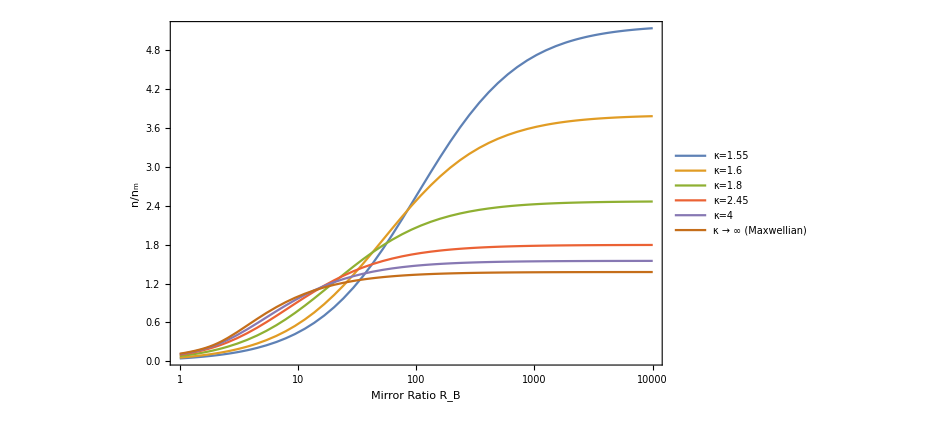

```mathematica
this=LogLinearPlot[{kappaGrate[RB,dPhi/Tm,155/100],kappaGrate[RB,dPhi/Tm,16/10],kappaGrate[RB,dPhi/Tm,18/10],kappaGrate[RB,dPhi/Tm,245/100],kappaGrate[RB,dPhi/Tm,4],MaxwellGrate[RB,dPhi/Tm]},{RB,1,10000},PlotRange->{All,All},PlotLegends->legends,LabelStyle->(FontSize->22),Frame->True,FrameStyle->Black,FrameLabel->{{StringForm["n/n_m"],""},{StringForm["Mirror Ratio R_B"],StringForm["ϕ̄= `1`",NumberForm[N[dPhi/Tm],{3,1}]]}},ImageSize->700]
```

## Now anuvver

```mathematica
{RB1,RB2,RB3,RB4}={3,30,300,1*^6};
```

```mathematica
kColors={Black,Blue,Orange};
```

```mathematica
plotStyles=Flatten@Table[Directive[color,lineStyle],{lineStyle,{Thick,Dashed,Dotted}},{color,kColors}];
```

```mathematica
nPlots=3;
```

```mathematica
legends=Style[#,FontSize->20]&/@{"κ=1.6","κ=2.45","κ → ∞ (Maxwellian)"}
If[nPlots>3,legends=legends~Join~Table["",{n,1,nPlots-3}]];
```

{κ=1.6,κ=2.45,κ → ∞ (Maxwellian)}

```mathematica
RBSinglePlot=RB2;
```

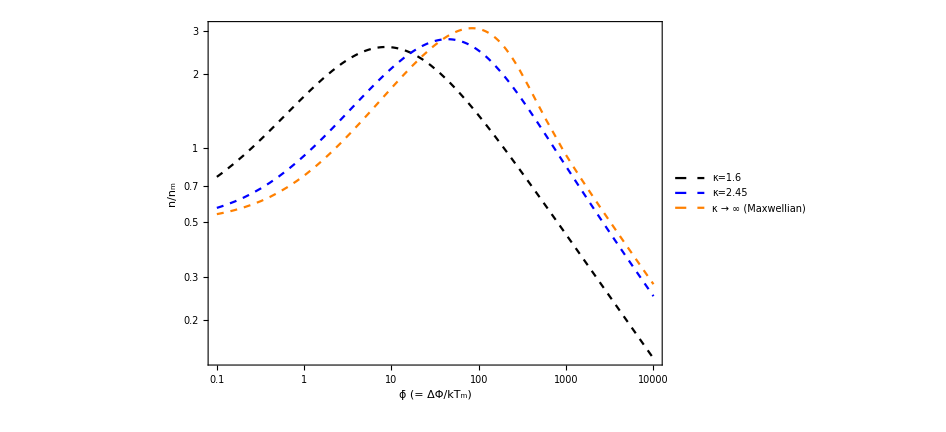

```mathematica
this2=LogLogPlot[
{kappaFac[RBSinglePlot,phiBar,16/10],kappaFac[RBSinglePlot,phiBar,245/100],LKMwellDensFac[phiBar,RBSinglePlot]},{phiBar,0.1,10000},PlotRange->{All,All},PlotStyle->plotStyles[[1;;nPlots]],PlotLegends->legends,LabelStyle->(FontSize->22),Frame->True,FrameStyle->Black,FrameLabel->{{StringForm["n/n_m"],""},{StringForm["ϕ̄ (= ΔΦ/kT_m)"],""}},ImageSize->700]
```

```mathematica
nPlots=9;
```

```mathematica
legends=Style[#,FontSize->20]&/@{"κ=1.6","κ=2.45","κ → ∞ (Maxwellian)"}
If[nPlots>3,legends=legends~Join~Table["",{n,1,nPlots-3}]];
```

{κ=1.6,κ=2.45,κ → ∞ (Maxwellian)}

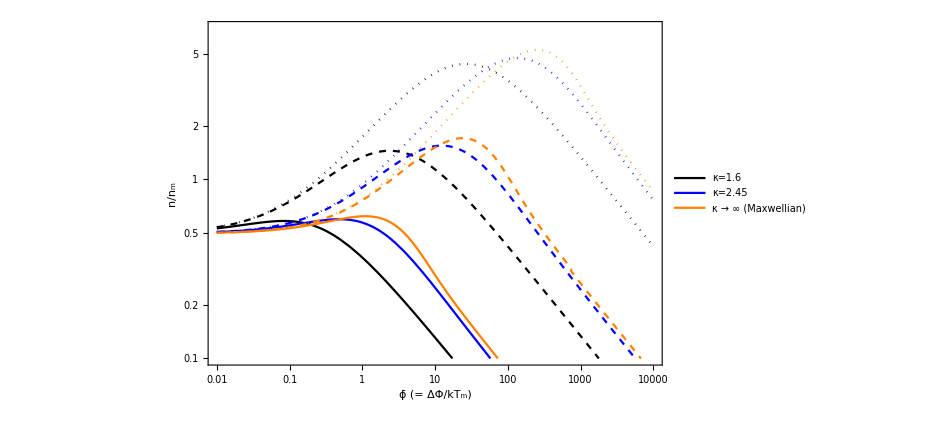

```mathematica
this2=LogLogPlot[
{kappaFac[RB1,phiBar,16/10],kappaFac[RB1,phiBar,245/100],LKMwellDensFac[phiBar,RB1],
kappaFac[RB2,phiBar,16/10],kappaFac[RB2,phiBar,245/100],LKMwellDensFac[phiBar,RB2],
kappaFac[RB3,phiBar,16/10],kappaFac[RB3,phiBar,245/100],LKMwellDensFac[phiBar,RB3]},{phiBar,0.01,10000},PlotRange->{All,{0.1,7}},PlotStyle->plotStyles[[1;;nPlots]],PlotLegends->legends,LabelStyle->(FontSize->22),Frame->True,FrameStyle->Black,FrameLabel->{{StringForm["n/n_m"],""},{StringForm["ϕ̄ (= ΔΦ/kT_m)"],""}},ImageSize->700]
```

```mathematica
this2=LogLogPlot[
{kappaFac[RBSinglePlot,phiBar,16/10],kappaFac[RBSinglePlot,phiBar,245/100],LKMwellDensFac[phiBar,RBSinglePlot]},{phiBar,0.1,10000},PlotRange->{All,All},PlotStyle->plotStyles[[1;;nPlots]],PlotLegends->legends,LabelStyle->(FontSize->22),Frame->True,FrameStyle->Black,FrameLabel->{{StringForm["n/n_m"],""},{StringForm["ϕ̄ (= ΔΦ/kT_m)"],""}},ImageSize->700]
```

```mathematica
this2=LogLinearPlot[
{kappaGrate[RB1,phiBar,16/RB1],kappaGrate[RB1,phiBar,245/100],MaxwellGrate[RB1,phiBar],
kappaGrate[10,phiBar,16/10],kappaGrate[RB2,phiBar,245/100],MaxwellGrate[RB2,phiBar],
kappaGrate[RB3,phiBar,16/10],kappaGrate[RB3,phiBar,245/100],MaxwellGrate[RB3,phiBar],
kappaGrate[RB4,phiBar,16/10],kappaGrate[RB4,phiBar,245/100],MaxwellGrate[RB4,phiBar]},{phiBar,1,10000},PlotRange->{All,All},PlotLegends->legends,LabelStyle->(FontSize->22),Frame->True,FrameLabel->{{StringForm["n/n_m"],""},{StringForm["Mirror Ratio R_B"],""}},ImageSize->700]
```